# Treemap

## 2013-02-22 Jeffrey Starr

## Abstract

Prior to implementing a treemap visualization in nvd3, this notebook will implement and test the treemap algorithm in order to demonstrate my understanding of the system.

## Data

Treemaps represent hierarchical data. Hierarchical data can be modeled as a tree, where each node represents a grouping of the data or, in the case of terminal nodes, the “size”  or “count” of that grouping.

Data is provided as a list of lists, with the individual child lists containing a sequence of vertex labels (categories) and the final value in the list being a weight (number). For example:

```mathematica
smallSampleData={{"a","c",3},{"a","d",4},{"b","c",2},{"b","d",6}};
```

All child lists must be of the same length and each path must be unique.

These child lists will be translated into a recursive list structure. The first element of each list will be the node name (with the top element being root) and the second element will either be a list of child nodes or a number for the weight.

```mathematica
ToRecursiveTreeForm[paths_]:=
{"root",ChildrenOf[paths]}
```

```mathematica
ChildrenOf[paths_]:=
Switch[Length[First[paths]],
2,
Table[path,{path,paths}],
_,With[{heads=Union[First[#]&/@paths]},
{#,
ChildrenOf[Cases[paths,{#,rest__}->{rest}]]}&/@heads
]
]
```

```mathematica
ToRecursiveTreeForm[smallSampleData]
```

{root,{{a,{{c,3},{d,4}}},{b,{{c,2},{d,6}}}}}

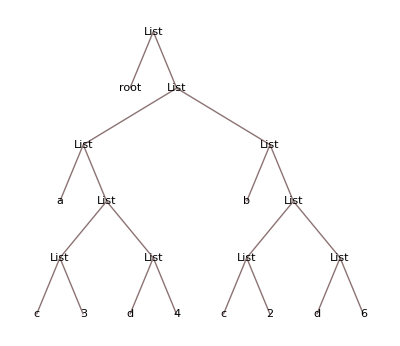

```mathematica
TreeForm[%95]
```

## Accessing Information

```mathematica
ChildrenArea[{_String,weight_}]:=weight
```

```mathematica
ChildrenArea[{_String,children_List}]:=
Total[ChildrenArea[#]&/@children]
```

```mathematica
ChildrenArea[ToRecursiveTreeForm[smallSampleData]]
```

15

### Rectangles

Mathematica provides a Rectangle object, which is defined by the pair of points (x_min,y_min) and (x_max,y_max). We provide a few useful functions:

```mathematica
Width[Rectangle[{xmin_,ymin_},{xmax_,ymax_}]]:=Abs[xmax-xmin]
```

```mathematica
Height[Rectangle[{xmin_,ymin_},{xmax_,ymax_}]]:=Abs[ymax-ymin]
```

```mathematica
Area[r_Rectangle]:=
Width[r]×Height[r]
```

```mathematica
RectLeft[Rectangle[{xmin_,ymin_},{xmax_,ymax_}]]:=xmin
```

```mathematica
RectRight[Rectangle[{xmin_,ymin_},{xmax_,ymax_}]]:=xmax
```

```mathematica
RectTop[Rectangle[{xmin_,ymin_},{xmax_,ymax_}]]:=ymax
```

```mathematica
RectBottom[Rectangle[{xmin_,ymin_},{xmax_,ymax_}]]:=ymin
```

```mathematica
Area[Rectangle[{1,3},{4,9}]]
```

18

The aspect ratio of a rectangle is the ratio of the longer edge to the shorter edge. If either edge has a zero length, this function returns infinity.

```mathematica
RectAspectRatio[r_Rectangle]:=
If[Width[r]==0∨Height[r]==0,∞,
If[Width[r]>Height[r],Width[r]/Height[r],Height[r]/Width[r]
]
]
```

```mathematica
RectAspectRatio[Rectangle[{0,0},{3/2,4}]]
```

8/3

Subrectangles may be placed in either Horizontal or Vertical orientation. This function flips between the two.

```mathematica
InvertOrientation[Horizontal]:=Vertical
```

```mathematica
InvertOrientation[Vertical]:=Horizontal
```

## Filling in a Rectangle

The squarified algorithm works by recursively filling in rectangles with smaller rectangles by balancing the aspect ratio of the filled in area.

This function returns a list of sub-rectangles given a list of areas (the list of areas must be less than or equal to the area of the parent rectangle) and an orientation.

```mathematica
FillRectangle[parent_Rectangle,{},Vertical]:={}
```

```mathematica
FillRectangle[parent_Rectangle,areas_List,Vertical]:=
Block[{heights=Prepend[Height[parent]*Accumulate[areas]/Total[areas],0]},
Table[
Rectangle[
{RectLeft[parent],
RectBottom[parent]+heights[[i]]},{RectLeft[parent]+areas[[i]]/(heights[[i+1]]-heights[[i]]),RectBottom[parent]+heights[[i+1]]}],
{i,Length[heights]-1}
]
]
```

```mathematica
FillRectangle[parent_Rectangle,{},Horizontal]:={}
```

```mathematica
FillRectangle[parent_Rectangle,areas_List,Horizontal]:=
Block[{widths=Prepend[Width[parent]*Accumulate[areas]/Total[areas],0]},
Table[
Rectangle[
{RectLeft[parent]+widths[[i]],
RectBottom[parent]},
{RectLeft[parent]+widths[[i+1]],RectBottom[parent]+areas[[i]]/(widths[[i+1]]-widths[[i]])}],
{i,Length[widths]-1}
]
]
```

### Test Fill

```mathematica
FillRectangle[Rectangle[{0,0},{6,4}],{6},Vertical]
```

{Rectangle[{0,0},{3/2,4}]}

```mathematica
FillRectangle[Rectangle[{0,0},{6,4}],{6,6},Vertical]
```

{Rectangle[{0,0},{3,2}],Rectangle[{0,2},{3,4}]}

```mathematica
FillRectangle[Rectangle[{0,0},{6,4}],{6,6,4},Vertical]
```

{Rectangle[{0,0},{4,3/2}],Rectangle[{0,3/2},{4,3}],Rectangle[{0,3},{4,4}]}

```mathematica
FillRectangle[Rectangle[{3/2,0},{6,4}],{4},Horizontal]
```

{Rectangle[{3/2,0},{6,8/9}]}

```mathematica
FillRectangle[Rectangle[{3,0},{6,4}],{4,3},Horizontal]
```

{Rectangle[{3,0},{33/7,7/3}],Rectangle[{33/7,0},{6,7/3}]}

## Visualize Iterative Rectangles

Given a list of rectangles, create a graphic.

```mathematica
VizRectangles[rectangles_List]:=
Graphics[
Join[
{EdgeForm[{Thick,Black}],
Opacity[7/10]},
Riffle[rectangles,ColorData["Crayola","ColorList"]]
],
Axes->True,
GridLines->Automatic
]
```

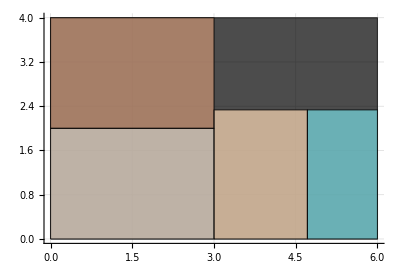

```mathematica
VizRectangles[{Rectangle[{0,0},{6,4}],Rectangle[{0,0},{3,2}],Rectangle[{0,2},{3,4}],Rectangle[{3,0},{33/7,7/3}],Rectangle[{33/7,0},{6,7/3}]}]
```

## Squarified Treemap Algorithm

As a heuristic, the squarified treemap algorithm adds child rectangles to the parent (within a given orientation, either Vertical or Horizontal) until the maximum aspect ratio of the children is greater than current step.

```mathematica
WorstAspectRatio[rectangles_]:=
Max[RectAspectRatio[#]&/@rectangles]
```

### Test WorstAspectRatio

```mathematica
WorstAspectRatio[{Rectangle[{0,0},{3/2,4}]}]
```

8/3

```mathematica
WorstAspectRatio[{Rectangle[{0,0},{3,2}],Rectangle[{0,2},{3,4}]}]
```

3/2

```mathematica
WorstAspectRatio[{Rectangle[{0,0},{4,3/2}],Rectangle[{0,3/2},{4,3}],Rectangle[{0,3},{4,4}]}]
```

4

### Placing till a Local Minima

As previously stated, the algorithm works by iteratively placing rectangles until a local minima of WorstAspectRatio is met. The function PlaceTillLocalMinima returns a list of rectangles placed into a given parent rectangle with a list (pre-sorted in descending order) of areas.

```mathematica
PlaceTillLocalMinima[parent_Rectangle,areas_List,orientation_]:=
PlaceTillLocalMinima[parent,areas,orientation,∞,0]
```

```mathematica
PlaceTillLocalMinima[parent_Rectangle,areas_List,orientation_,previousRatio_,prevTake_]:=
If[prevTake+1<=Length[areas],
Block[{take=FillRectangle[parent,Take[areas,prevTake+1],orientation]},
If[WorstAspectRatio[take]<previousRatio,
PlaceTillLocalMinima[parent,areas,orientation,WorstAspectRatio[take],prevTake+1],
FillRectangle[parent,Take[areas,prevTake],orientation]
]
],
FillRectangle[parent,areas,orientation]
]
```

#### Test Placing till a Local Minima

```mathematica
PlaceTillLocalMinima[Rectangle[{0,0},{6,4}],{6,6,4,3,2,2,1},Vertical]
```

{Rectangle[{0,0},{3,2}],Rectangle[{0,2},{3,4}]}

```mathematica
PlaceTillLocalMinima[Rectangle[{3,0},{6,4}],{4,3,2,1,1},Horizontal]
```

{Rectangle[{3,0},{33/7,7/3}],Rectangle[{33/7,0},{6,7/3}]}

### Finding Remainder

Once a set of sub-rectangles has been added to a parent, the next step will be to calculate the remaining portion of the parent. This function takes advantage of the fact that the children will be a subset of the parent -- no overlap and the children will themselves form a rectangle.

```mathematica
EnclosingRectangle[rectangles_]:=
Rectangle[
{Min[RectLeft[#]&/@rectangles],Min[RectBottom[#]&/@rectangles]},
{Max[RectRight[#]&/@rectangles],Max[RectTop[#]&/@rectangles]}
]
```

```mathematica
RemainingRectangle[
Rectangle[{pxmin_,pymin_},{pxmax_,pymax_}],Rectangle[{cxmin_,cymin_},{cxmax_,cymax_}]]:=
Switch[
{pxmin==cxmin∧pxmax==cxmax,pymin==cymin∧pymax==cymax},
{False,False} (* child NOT a subset of parent *),
Abort[],
{False,True}(* remainder on right *),
Rectangle[{cxmax,pymin},{pxmax,pymax}],
{True,False}(* remainder on top *),
Rectangle[{pxmin,cymax},{pxmax,pymax}],
{True,True}(* child == parent, no remainder *),
Rectangle[{pxmax,pymax},{pxmax,pymax}]
]
```

#### Test Finding Remainder

```mathematica
EnclosingRectangle[{Rectangle[{0,0},{3,2}],Rectangle[{0,2},{3,4}]}]
```

Rectangle[{0,0},{3,4}]

```mathematica
RemainingRectangle[Rectangle[{0,0},{6,4}],Rectangle[{0,0},{3,4}]]
```

Rectangle[{3,0},{6,4}]

```mathematica
RemainingRectangle[Rectangle[{3,0},{6,4}],EnclosingRectangle[{Rectangle[{3,0},{33/7,7/3}],Rectangle[{33/7,0},{6,7/3}]}]]
```

Rectangle[{3,7/3},{6,4}]

```mathematica
RemainingRectangle[Rectangle[{0,0},{1,1}],Rectangle[{0,0},{1,1}]]
```

Rectangle[{1,1},{1,1}]

## Squarify

With all the pieces together, we can now write the Squarify function. This function takes the definition of a parent rectangle and a list of areas (whose sum must equal the area of the parent) and returns a list of Rectangles.

```mathematica
Squarify[parent_Rectangle,areas_List]:=
Squarify[parent,areas,{},Vertical]
```

```mathematica
Squarify[parent_Rectangle,areas_List,placed_List,orientation_]:=
If[Length[areas]==0,placed,
Block[
{placeThisStep=PlaceTillLocalMinima[parent,areas,orientation]},
Squarify[
RemainingRectangle[parent,EnclosingRectangle[placeThisStep]],
Drop[areas,Length[placeThisStep]],
Join[placed,placeThisStep],
InvertOrientation[orientation]
]
]
]
```

```mathematica
Squarify[Rectangle[{0,0},{6,4}],{6,6,4,3,2,2,1}]
```

{Rectangle[{0,0},{3,2}],Rectangle[{0,2},{3,4}],Rectangle[{3,0},{33/7,7/3}],Rectangle[{33/7,0},{6,7/3}],Rectangle[{3,7/3},{21/5,4}],Rectangle[{21/5,7/3},{6,31/9}],Rectangle[{21/5,31/9},{6,4}]}

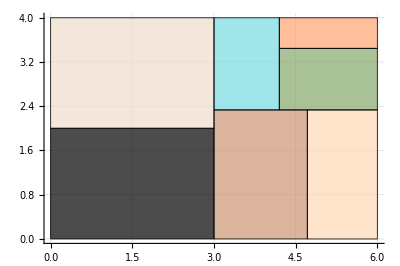

```mathematica
VizRectangles[%47]
```